```mathematica
(*FFT算弹簧摆的能谱*)
```

{2012,7,18,16,42,39.8956}

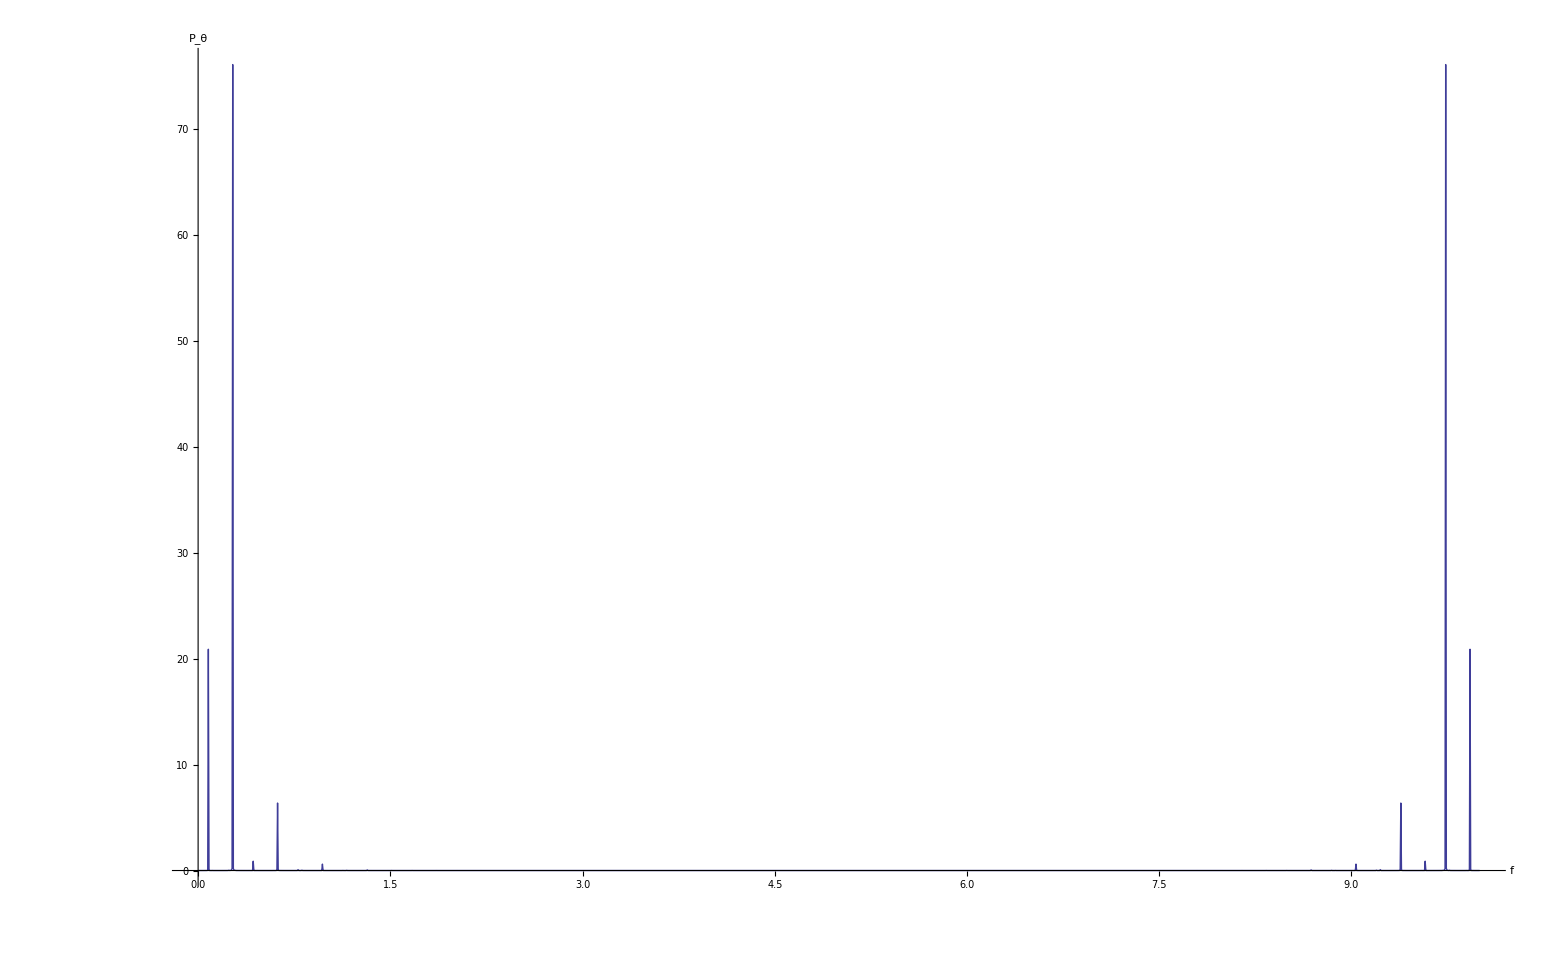

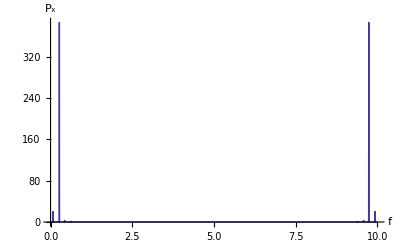

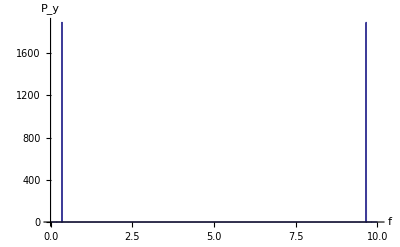

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=200.0;xinitial={0,1.3};yinitial={-L0,0};Date[]
equs={m x''[t]==-k(1-L0/(√(x[t]^2+y[t]^2)))x[t],m y''[t]==k(-1+L0/(√(x[t]^2+y[t]^2)))y[t]-m g,x[0]==xinitial[[1]],x'[0]==xinitial[[2]],y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
θ[t_]:=Arg[-y[t]+x[t]ⅈ];
sample=2000;
signal=Table[θ[t],{t,0,tm,tm/sample}];
θpsFFT=(Abs[Fourier[signal]])^2;len=Length[θpsFFT];θpsFFT=Table[{(k-1)/tm,θpsFFT[[k]]},{k,1,len}];
ListLinePlot[θpsFFT,PlotRange->{{0,10},All},AxesLabel->{"f","P_θ"},BaseStyle->{FontSize->13}]
signal=Table[x[t],{t,0,tm,tm/sample}];
xpsFFT=(Abs[Fourier[signal]])^2;len=Length[xpsFFT];xpsFFT=Table[{(k-1)/tm,xpsFFT[[k]]},{k,1,len}];
ListLinePlot[xpsFFT,PlotRange->{{0,10},All},AxesLabel->{"f","P_x"},BaseStyle->{FontSize->13}]
average=Sum[y[t],{t,0,tm,tm/sample}]/sample;
signal=Table[y[t]-average,{t,0,tm,tm/sample}];
ypsFFT=(Abs[Fourier[signal]])^2;len=Length[ypsFFT];ypsFFT=Table[{(k-1)/tm,ypsFFT[[k]]},{k,1,len}];
ListLinePlot[ypsFFT,PlotRange->{{0,10},All},AxesLabel->{"f","P_y"},BaseStyle->{FontSize->13}]
```